```mathematica
Remove["Global`*"]
soln[t_]:=DSolve[{x''[t]==a,x'[0]==v0,x[0]==x0}, x[t], t]//Simplify
Print["x[t]= ", x[t]/.soln[t]]
```

x[t]= {(a t^2)/2+t v0+x0}

```mathematica
(* Solve the following for x1(t) and x2(t):mx¨1+2kx1−kx2=0 mx¨2+2kx2−kx1=0
x˙1(0)=0 ˙x2(0)=0 x1(0)=0 x2(0)=a *)
Remove["Global`*"]

eq1:=m x1''[t]+2k x1[t]-k x2[t]==0
eq2:=m x2''[t]+2k x2[t]-k x1[t]==0

ic:={x1'[0]==0,x2'[0]==0,x1[0]==0,x2[0]==a}



solns=DSolve[{eq1,eq2,ic},{ x1[t],x2[t]},t][[1]]//FullSimplify;

Print["x1[t]= ",x1[t]/. solns]
Print["x2[t]= ",x2[t]/. solns]
```

x1[t]= 1/2 a (Cos[(√k t)/(√m)]-Cos[(√3 √k t)/(√m)])

x2[t]= 1/2 a (Cos[(√k t)/(√m)]+Cos[(√3 √k t)/(√m)])

x1[t]= -(a ⅇ^(-t (β+√(β^2-ω0^2))) ((-1+ⅇ^(2 t √(β^2-ω0^2))) β+(1+ⅇ^(2 t √(β^2-ω0^2))-2 ⅇ^(t (β+√((β-ω0) (β+ω0))))) √(β^2-ω0^2)))/(2 ω0^2 √((β-ω0) (β+ω0)))

x2[t]= 1/(2 ω0^2 √(β^2-ω0^2))a ⅇ^(-f τ0 (-β+√(β^2-ω0^2))-f τ0 (β+√(β^2-ω0^2))) (-ⅇ^(2 f τ0 √(β^2-ω0^2)+t (-β+√(β^2-ω0^2))) β+ⅇ^(t (-β+√(β^2-ω0^2))+f τ0 (β+√(β^2-ω0^2))) β+ⅇ^(t (-β-√(β^2-ω0^2))+f τ0 (-β+√(β^2-ω0^2))+f τ0 (β+√(β^2-ω0^2))) β-ⅇ^(t (-β-√(β^2-ω0^2))+f τ0 (-β+√(β^2-ω0^2))+2 f τ0 (β+√(β^2-ω0^2))) β-ⅇ^(2 f τ0 √(β^2-ω0^2)+t (-β+√(β^2-ω0^2))) √(β^2-ω0^2)+ⅇ^(t (-β+√(β^2-ω0^2))+f τ0 (β+√(β^2-ω0^2))) √(β^2-ω0^2)-ⅇ^(t (-β-√(β^2-ω0^2))+f τ0 (-β+√(β^2-ω0^2))+f τ0 (β+√(β^2-ω0^2))) √(β^2-ω0^2)+ⅇ^(t (-β-√(β^2-ω0^2))+f τ0 (-β+√(β^2-ω0^2))+2 f τ0 (β+√(β^2-ω0^2))) √(β^2-ω0^2))

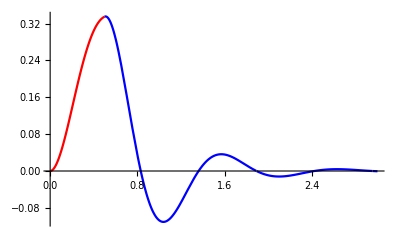

```mathematica
Remove["Global`*"]
t0=0;
t1=f τ0;
eq1[t_]:=x1''[t]+2 β x1'[t]+ω0 ^2x1[t] ==a 
eq2[t_]:=x2''[t]+2β x2'[t]+ω0 ^2 x2[t]==0


ic1:={x1[0]==0 , x1'[0]==0}
bc:={x1[t1]==x2[t1], x1'[t1]==x2'[t1]}
soln1=DSolve[{eq1[t],ic1},{x1[t]}, t][[1]]//FullSimplify;
x1[t_]=x1[t]/.soln1//FullSimplify;
soln2=DSolve[{eq2[t], bc},{x2[t]}, t][[1]];
x2[t_]=x2[t]/.soln2;
Print["x1[t]= ", x1[t]]
Print["x2[t]= ", x2[t]]


β=ω0/3 ; a=10 ;f=.5;τ0=1; t2=3; ω0=(2  π)/τ0;

plot1:=Plot[x1[t], {t, t0, t1},PlotRange->All, PlotStyle->Red];
plot2:=Plot[x2[t], {t, t1, t2}, PlotRange->All, PlotStyle->Blue];
Show[plot1, plot2]
```

```mathematica
Remove["Global`*"]
SetAttributes[{L,g,m1,m2},Constant];
U= (1/2) k(x2[t]-x1[t]-L)^2;
T=(1/2)m1(x1'[t])^2+(1/2)m2 (x2'[t])^2 ;
lag= T-U;
Print["Lagrangian = ", lag]
x1[t_]=q1[t];
x2[t_]=q2[t]+L;
Print["Lagrangian = ", lag]
(* Euler- Lagrange *)
EL[q_]:=D[lag,q] - Dt[  D[lag,D[q,t]],t]==0;
(*Equations of Motion*)
Print["Equation of motion 1 is: "EL[q1[t]]//Simplify]
Print["Equation of motion 2 is: "EL[q2[t]]//Simplify]
ic={q1[0]==0,q2[0]==0,q1'[0]==1, q2'[0]==-1};
list={EL[q1[t]],EL[q2[t]]};
DSolve[{list, ic},{q1[t],q2[t]},t]//ExpToTrig
```

Lagrangian = -1/2 k (-L-x1[t]+x2[t])^2+1/2 m1 x1'[t]^2+1/2 m2 x2'[t]^2

Lagrangian = -1/2 k (-q1[t]+q2[t])^2+1/2 m1 q1'[t]^2+1/2 m2 q2'[t]^2

Equation of motion 1 is:  (k q1[t]+m1 q1''[t]==k q2[t])

Equation of motion 2 is:  (k q1[t]==k q2[t]+m2 q2''[t])

{{q1[t]→-1/((m1+m2) √(-k m1^2 m2-k m1 m2^2))(Cosh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]-Sinh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]) (m1 m2^2-m1 √(-k m1^2 m2-k m1 m2^2) t Cosh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]+m2 √(-k m1^2 m2-k m1 m2^2) t Cosh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]-m1 m2^2 Cosh[(2 √(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]-m1 √(-k m1^2 m2-k m1 m2^2) t Sinh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]+m2 √(-k m1^2 m2-k m1 m2^2) t Sinh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]-m1 m2^2 Sinh[(2 √(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]),q2[t]→-1/((m1+m2) √(-k m1^2 m2-k m1 m2^2))(Cosh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]-Sinh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]) (-m1^2 m2-m1 √(-k m1^2 m2-k m1 m2^2) t Cosh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]+m2 √(-k m1^2 m2-k m1 m2^2) t Cosh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]+m1^2 m2 Cosh[(2 √(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]-m1 √(-k m1^2 m2-k m1 m2^2) t Sinh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]+m2 √(-k m1^2 m2-k m1 m2^2) t Sinh[(√(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)]+m1^2 m2 Sinh[(2 √(-k m1^2 m2-k m1 m2^2) t)/(m1 m2)])}}

```mathematica
Remove["Global`*"]
SetAttributes[{L,g,m},Constant];

T=(1/2) m((x1'[t])^2 + (x2'[t])^2+(y1'[t])^2+(y2'[t])^2);
U=m g(y1[t]+y2[t]);
lag=T-U;
Print["Lagrangian = ", lag//FullSimplify]
x1[t_]=L Sin[θ1[t]]; 
y1[t_]=-L Cos[θ1[t]];
x2[t_]=x1[t]+L Sin[θ2[t]];
y2[t_]=y1[t]-L Cos[θ2[t]];
Print["Lagrangian = ", lag//FullSimplify]
(* Euler- Lagrange *)
EL[q_]:=D[lag,q] - Dt[  D[lag,D[q,t]],t]==0;
Print["The equation of motion for pendulum 1 is: "EL[θ1[t]]//Simplify]
Print["The equation of motion for pendulum 2 is: "EL[θ2[t]]//Simplify]
```

Lagrangian = 1/2 m (-2 g (y1[t]+y2[t])+x1'[t]^2+x2'[t]^2+y1'[t]^2+y2'[t]^2)

Lagrangian = 1/2 L m (2 g (2 Cos[θ1[t]]+Cos[θ2[t]])+L (2 θ1'[t]^2+2 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+θ2'[t]^2))

The equation of motion for pendulum 1 is:  (L m (2 g Sin[θ1[t]]+L Sin[θ1[t]-θ2[t]] θ2'[t]^2+2 L θ1''[t]+L Cos[θ1[t]-θ2[t]] θ2''[t])==0)

The equation of motion for pendulum 2 is:  (L m (g Sin[θ2[t]]-L Sin[θ1[t]-θ2[t]] θ1'[t]^2+L Cos[θ1[t]-θ2[t]] θ1''[t]+L θ2''[t])==0)